```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Folgendes Integral soll minimiert bzw. maximiert (Vorzeichen des Integrandens wird invertiert) werden:

ℐ=∫_t_1^t_2 F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→min , bzw.  ℐ=∫_t_1^t_2 -F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→max

In dem Funktionenvektor 𝓏_1 sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) vorkommen.
In dem Funktionenvektor 𝓏_2 hingegen sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) nicht vorkommen. 𝓏_2 ist in der Regel ausschließlich im 3. Fall vorhanden!

3. Fall: Ein weiteres Differentialgleichungssystem (𝓏̇)_1=𝒻(t,𝓏_1,𝓏_2) soll erfüllt werden (falls eine oder mehrere Differentialgleichungen höherer Ordnung auftreten, müssen diese zunächst in Differentialgleichungssysteme höheren Grades umgewandelt und zu einem Differentialgleichungssystem zusammengefasst werden).

Für das resultierende Differentialgleichungssystem gilt (λ ist im Gegensatz zum 2. Fall keine Konstante, sondern ein Vektor):

H(t,𝓏_1, (𝓏̇)_1,𝓏_2,λ)=F(t,𝓏_1, (𝓏̇)_1,𝓏_2)+𝒻[t,𝓏_1,𝓏_2]^T·λ
ⅆ/ⅆt (0
λ
𝓏_1)=(∇_𝓏_2 
-∇_𝓏_1
∇_λ ) H(t,𝓏_1, (𝓏̇)_1,𝓏_2,λ)

## Eingabe (F, 𝓏_1, 𝓏_2, 𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃, 𝒻)

```mathematica
ClearAll["Global`*"]
F[t_]=D[x[t],t]^2+y[t]^2;
𝓏1[t_]={x[t],v[t]};
𝓏2[t_]={y[t]};
𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃={x[0]==0,x[1/4]==0,v[0]==1,v[1/4]==1};
𝒻[t_]={v[t],-2v[t]-π^2 x[t]-y[t]};
λ[t_]={λ1[t],λ2[t]};
```

## Programm (manuell)

```mathematica
H[t_]=F[t]+𝒻[t].λ[t];
𝓏[t_]=Join[𝓏1[t],𝓏2[t],λ[t]];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ1=Table[
FullSimplify[Grad[H[t],𝓏2[t]][[i]]==0],
{i,Length[𝓏2[t]]}];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ2=Table[
FullSimplify[-Grad[H[t],𝓏1[t]][[i]]==D[λ[t],t][[i]]],
{i,Length[𝓏1[t]]}];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ3=Table[
FullSimplify[Grad[H[t],λ[t]][[i]]==D[𝓏1[t],t][[i]]],
{i,Length[𝓏1[t]]}];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ=Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ1,𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ2,𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ3];

𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm
```

2 y[t]==λ2[t]
π^2 λ2[t]==λ1'[t]
λ1[t]+λ2'[t]==2 λ2[t]
v[t]==x'[t]
2 v[t]+π^2 x[t]+y[t]+v'[t]==0

λ_2=2y
ⅆ/ⅆt(λ_1
2y
x
v)=(2 π^2 y
4y-λ_1
v
-y-π^2 x-2v)
ⅆ/ⅆt(λ_1
y
x
v)=(2 π^2 y
2y-λ_1/2
v
-y-π^2 x-2v)

```mathematica
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ={
D[λ1[t],t]==2 π^2 y[t],
D[y[t],t]==2y[t]-λ1[t]/2,
D[x[t],t]==v[t],
D[v[t],t]==-y[t]-π^2 x[t]-2v[t]};

𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm
```

λ1'[t]==2 π^2 y[t]
y'[t]==2 y[t]-λ1[t]/2
x'[t]==v[t]
v'[t]==-2 v[t]-π^2 x[t]-y[t]

## DGL

```mathematica
𝓎[t_]=Flatten[FullSimplify[N[DSolve[Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ,𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],{y[t],x[t],v[t],λ1[t]},t]]]]
```

{v[t]→ⅇ^((-1.-2.97819 ⅈ) t) ((3.20093-8.5916 ⅈ)+(3.20093+8.5916 ⅈ) ⅇ^((0.+5.95638 ⅈ) t)-(2.70093-6.60991 ⅈ) ⅇ^(2. t)-(2.70093+6.60991 ⅈ) ⅇ^((2.+5.95638 ⅈ) t)),x[t]→ⅇ^((-1.-2.97819 ⅈ) t) ((2.26822+1.8364 ⅈ)+(2.26822-1.8364 ⅈ) ⅇ^((0.+5.95638 ⅈ) t)-(2.26822+0.14529 ⅈ) ⅇ^(2. t)-(2.26822-0.14529 ⅈ) ⅇ^((2.+5.95638 ⅈ) t)),y[t]→(10.8037-26.4396 ⅈ) ⅇ^((1.-2.97819 ⅈ) t)+(10.8037+26.4396 ⅈ) ⅇ^((1.+2.97819 ⅈ) t),λ1[t]→(179.092+11.4716 ⅈ) ⅇ^((1.-2.97819 ⅈ) t)+(179.092-11.4716 ⅈ) ⅇ^((1.+2.97819 ⅈ) t)}

## Plot

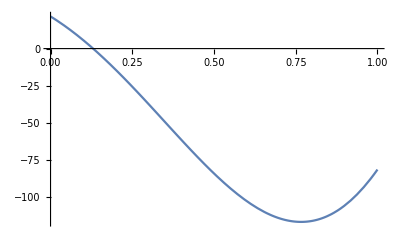

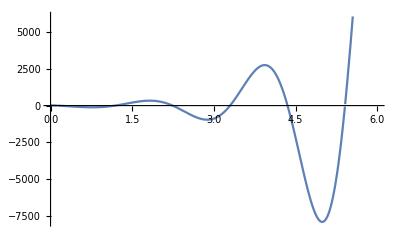

```mathematica
Plot[𝓎[t][[3,2]],{t,0,1}]
Plot[𝓎[t][[3,2]],{t,0,6}]
```